```mathematica
Import[NotebookDirectory[]<>"multiband.wl"]
```

```mathematica
Hmb[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ11=Δ0,Δ12=Δ0,H11,H12,H22,ϵ=0.75},H11=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H22=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(ϵ-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H12=KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ12*IdentityMatrix[dim,SparseArray]]];Chop@ArrayFlatten[{{H11,H12},{H12,H22}}]]
```

```mathematica
Hmbdis[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,vimp_,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ11=Δ0,Δ12=Δ0,H11,H12,H22,ϵ=1,mux},mux=μ-vimp;H11=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(+2*t)IdentityMatrix[dim,SparseArray]-DiagonalMatrix[mux]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H22=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(ϵ+2*t)IdentityMatrix[dim,SparseArray]-DiagonalMatrix[mux]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H12=KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ12*IdentityMatrix[dim,SparseArray]]];Chop@ArrayFlatten[{{H11,H12},{H12,H22}}]]
```

```mathematica
wfmajoranamb[a_,μ_,vz_,dim_,index_]:=Block[{testp,testn,gamma,test,gamma1,gamma2},testp=Transpose[Sort[Select[Transpose[Eigensystem[Hmb[a,μ,.2,vz,5,dim],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}]],#[[1]]>0&],#1[[1]]<#2[[1]]&][[1;;4]]];test1=testp[[2,All,1;;4dim]];test2=testp[[2,All,4dim+1;;8dim]];gamma11=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test1[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{1,3}]]],{i,index}];gamma12=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test1[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{2,4}]]],{i,index}];gamma21=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test2[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{1,3}]]],{i,index}];gamma22=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test2[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{2,4}]]],{i,index}];(*ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma11,gamma12,gamma21,gamma22}]],1],DataRange->{0,dim*a/100},PlotLabel->"V_Z="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,(*Filling->Axis,*)PlotLegends->Placed[SwatchLegend[{"1st γ_1 L","1st γ_2 L","1st γ_1 H","1st γ_2 H","2nd γ_1 L","2nd γ_2 L","2nd γ_1 H","2nd γ_2 H"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->(Directive[Thin,#]&/@{Blue,Cyan,Red,Orange,LightBlue,Green,LightRed,Purple})]*)Grid[{{ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma11,gamma12}]],1],DataRange->{0,dim*a/100},PlotLabel->"V_Z="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,(*Filling->Axis,*)PlotLegends->Placed[SwatchLegend[{"1st γ_1 L","1st γ_2 L","2nd γ_1 L","2nd γ_2 L","3rd γ_1 L","3rd γ_2 L","4th γ_1 L","4th γ_2 L"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->(Directive[Thin,#]&/@{Blue,Cyan,Red,Orange,Pink,Green,LightRed,Purple}),ImageSize->Medium],ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma21,gamma22}]],1],DataRange->{0,dim*a/100},PlotLabel->"V_Z="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,(*Filling->Axis,*)PlotLegends->Placed[SwatchLegend[{"1st γ_1 H","1st γ_2 H","2nd γ_1 H","2nd γ_2 H","3rd γ_1 H","3rd γ_2 H","4th γ_1 H","4th γ_2 H"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->(Directive[Thin,#]&/@{Blue,Cyan,Red,Orange,Pink,Green,LightRed,Purple}),ImageSize->Medium]}}]]
```

```mathematica
wfmajoranambdis[a_,μ_,vz_,dim_,vimp_,index_]:=Block[{testp,testn,gamma,test,gamma1,gamma2},testp=Transpose[Sort[Select[Transpose[Eigensystem[Hmbdis[a,μ,.2,vz,5,vimp,dim],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}]],#[[1]]>0&],#1[[1]]<#2[[1]]&][[1;;4]]];test1=testp[[2,All,1;;4dim]];test2=testp[[2,All,4dim+1;;8dim]];gamma11=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test1[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{1,3}]]],{i,index}];gamma12=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test1[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{2,4}]]],{i,index}];gamma21=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test2[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{1,3}]]],{i,index}];gamma22=Table[gamma=KroneckerProduct[1/2 ConjugateTranspose@{{1,I,0,0},{0,0,1,I},{0,0,1,-I},{-1,I,0,0}},IdentityMatrix[dim,SparseArray]].test2[[i]];Total[ArrayReshape[Abs[gamma]^2,{4,dim}][[{2,4}]]],{i,index}];(*ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma11,gamma12,gamma21,gamma22}]],1],DataRange->{0,dim*a/100},PlotLabel->"V_Z="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,(*Filling->Axis,*)PlotLegends->Placed[SwatchLegend[{"1st γ_1 L","1st γ_2 L","1st γ_1 H","1st γ_2 H","2nd γ_1 L","2nd γ_2 L","2nd γ_1 H","2nd γ_2 H"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->(Directive[Thin,#]&/@{Blue,Cyan,Red,Orange,LightBlue,Green,LightRed,Purple})]*)Grid[{{ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma11,gamma12}]],1],DataRange->{0,dim*a/100},PlotLabel->"V_Z="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,(*Filling->Axis,*)PlotLegends->Placed[SwatchLegend[{"1st γ_1 L","1st γ_2 L","2nd γ_1 L","2nd γ_2 L","3rd γ_1 L","3rd γ_2 L","4th γ_1 L","4th γ_2 L"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->(Directive[Thin,#]&/@{Blue,Cyan,Red,Orange,Pink,Green,LightRed,Purple}),ImageSize->Medium],ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma21,gamma22}]],1],DataRange->{0,dim*a/100},PlotLabel->"V_Z="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,(*Filling->Axis,*)PlotLegends->Placed[SwatchLegend[{"1st γ_1 H","1st γ_2 H","2nd γ_1 H","2nd γ_2 H","3rd γ_1 H","3rd γ_2 H","4th γ_1 H","4th γ_2 H"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->(Directive[Thin,#]&/@{Blue,Cyan,Red,Orange,Pink,Green,LightRed,Purple}),ImageSize->Medium]}}]]
```

```mathematica
vimplist=Flatten@Import["D:\\CMTC\\bothlead\\Rp12\\8\\m2v1.5L80.dat"]
```

{0.310975,3.66789,-0.656463,0.302498,1.71872,-1.52264,1.88148,-0.601242,1.24904,-0.800696,2.59606,1.7898,-1.02919,2.74381,-0.419159,1.20991,0.266816,-0.00730873,3.04649,-2.30793,-2.27617,1.21782,-3.24535,1.23248,1.96052,-2.2296,-0.0487891,-0.898144,1.39902,-0.949902,1.20568,-1.14646,1.6161,0.55922,-1.77883,-1.72664,0.0849731,-2.96707,1.37362,2.21469,0.992022,-1.72121,0.360728,3.35656,1.88652,0.818697,1.31117,2.01512,0.288113,-0.159774,-0.404665,0.242298,-0.348417,-1.14617,-1.39449,0.911801,-0.847666,-1.41177,-2.05701,-2.06035,1.02991,-0.546082,0.928577,1.82311,-0.400245,1.08818,4.34393,-0.503051,0.671414,-0.45821,1.67542,-0.600335,-0.62573,0.994469,-0.0326292,-1.02696,-3.25023,-2.1118,-0.810986,1.18247}

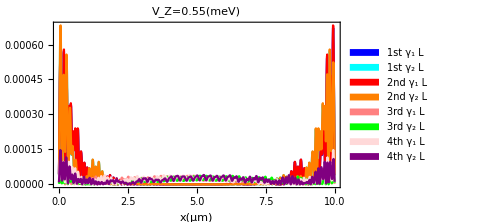
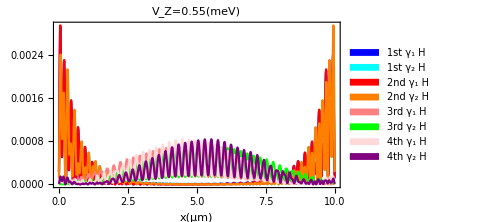
-Graphics- | -Graphics-

```mathematica
wfmajoranamb[1,2,0.55,1000,4]
```

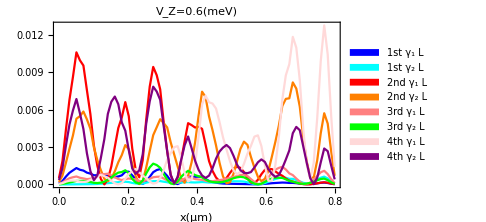
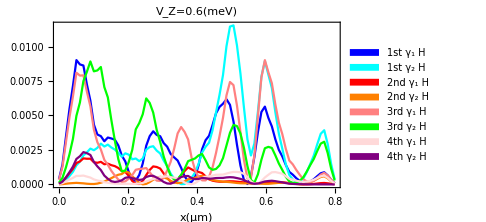
-Graphics- | -Graphics-

```mathematica
wfm=wfmajoranambdis[1,2,0.6,80,vimplist,4]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp12\\8\\m2.0D0.2a5Dc0.2ep0.75L80v1.5V0.6.png",wfm]
```

D:\CMTC\bothlead\Rp12\8\m2.0D0.2a5Dc0.2ep0.75L80v1.5V0.6.png

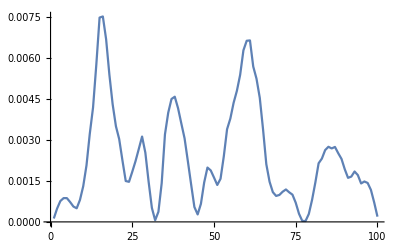

```mathematica
ListLinePlot[gamma11[[1]],PlotRange->Full]
```

```mathematica
Hmbp[μ0_,Δ0_,α0_,V0_]:=Block[{H11,H12,H22,H,Hmb22,Hmb11,Hmb12,η=25,k,μ=μ0,V=V0,α=α0,Δ=Δ0,Δc=.2,Hp,ϵ=0,sl,u=.5},H11=(η k^2 -μ)*IdentityMatrix[2]+V PauliMatrix[3]-α k PauliMatrix[2];H12=Δ IdentityMatrix[2];H22=-(η k^2 -μ)*IdentityMatrix[2]+V PauliMatrix[3]+α k PauliMatrix[2];H=ArrayFlatten[{{H11,H12},{H12,H22}}];Hmb22=ArrayFlatten[{{(η k^2 -(μ-ϵ))*IdentityMatrix[2]+V PauliMatrix[3]-α k PauliMatrix[2],Δ IdentityMatrix[2]},{Δ IdentityMatrix[2],-(η k^2 -(μ-ϵ))*IdentityMatrix[2]+V PauliMatrix[3]+α k PauliMatrix[2]}}];Hmb11=H;Hmb12=KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]]Δc;Hp=ArrayFlatten[{{Hmb11,Hmb12},{Hmb12,Hmb22}}];sl=Eigenvalues[Hp];ListLinePlot[Transpose@Table[sl,{k,-u,u,.01}],DataRange->{-u,u},PlotRange->{{-u,u},{0,2}},PlotStyle->{Blue,LightBlue,Red,LightRed},PlotLabel->sl[[5]]/.k->0]]
```

```mathematica
Manipulate[Hmbp[μx,Δx,αx,Vx],{μx,0,2},{Δx,0,0.2},{αx,1,3},{Vx,0,2},SaveDefinitions->True]
```

```mathematica
data=Block[{vzm=1,vzstep=0.02,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[Hmb[1,μ,Δ,vz,α,3000],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

{0.183305,0.168786,0.148913,0.128916,0.108918,0.088922,0.0689275,0.0489371,0.0289591,0.00906687,1.46765×10^-10,0.0311508,2.22027×10^-15,8.06606×10^-16,5.15333×10^-16,9.37392×10^-16,0.116922,1.68691×10^-15,2.57346×10^-15,1.08775×10^-15,6.74942×10^-16,1.40315×10^-15,1.09174×10^-15,0.102617,1.49365×10^-15,1.24246×10^-15,0.0978952,7.84529×10^-16,8.35001×10^-17,1.44592×10^-16,6.96223×10^-16,2.59744×10^-17,1.32033×10^-15,1.0514×10^-16,3.51146×10^-16,4.43908×10^-16,7.45994×10^-16,5.7622×10^-15,7.75079×10^-15,1.92788×10^-14,3.97775×10^-14,8.0705×10^-14,1.52402×10^-13,2.88742×10^-13,5.01973×10^-13,8.00642×10^-13,1.04111×10^-12,8.43495×10^-13,6.012×10^-13,3.45168×10^-15,3.33277×10^-15}

```mathematica
data=Block[{vzm=1,vzstep=0.02,μ=0.1,α=2,Δ=0.2},ParallelTable[{vz,Min@Abs@Eigenvalues[Hmb[1,μ,Δ,vz,α,3000],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}]},{vz,0,vzm,vzstep}]]
```

```mathematica
data2=Block[{vzm=1,vzstep=0.01,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

```mathematica
Dynamic[vz]
```

```mathematica
data//Length
```

```mathematica
ListLinePlot[data,PlotRange->Full]
```

### Δ12=.05meV

```mathematica
delta120p05=Import[NotebookDirectory[]<>"\\deltac0.05.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p05
```

### Δ12=.1meV

```mathematica
delta120p1=Import[NotebookDirectory[]<>"\\deltac0.1.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p1
```

```mathematica
ListDensityPlot[delta120p1,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

### Δ12=.15meV

```mathematica
delta120p15=Import[NotebookDirectory[]<>"\\deltac0.15.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p15
```

### Δ12=.2meV

```mathematica
delta120p2=Import[NotebookDirectory[]<>"\\deltac0.2.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p2
```

```mathematica
ListDensityPlot[delta120p2,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

```mathematica
bottom=Import[NotebookDirectory[]<>"\\b.dat"];
```

```mathematica
upper=Import[NotebookDirectory[]<>"\\u.dat"];
```

```mathematica
ListDensityPlot[bottom,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

```mathematica
ListDensityPlot[upper,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"},PlotRange->Full]
```

```mathematica
MapThread[ListLinePlot[{#1,#2,#3},PlotRange->Full,Frame->True,DataRange->{0,1},PlotStyle->{Blue,Red,Green},PlotLabel->ToString@#4]&,{bottom,upper,delta120p2,Range[0,2,.05]}]
```

### Δ12=.3meV

```mathematica
delta120p3=Import[NotebookDirectory[]<>"\\deltac0.3.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p3
```

### Δ12=.4meV

```mathematica
delta120p4=Import[NotebookDirectory[]<>"\\deltac0.4.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p4
```

```mathematica
ListDensityPlot[delta120p3,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

### μ from 0-2

```mathematica
muvaries=Table[Import["D:\\Nanowire\\Conductance\\Data\\"<>"mu"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.dat"],{i,0.0,2.0,0.05}];
```

```mathematica
Dynamic[i]
```

```mathematica
fnmuvaries=Table["mu"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png",{i,0.0,2.0,0.05}]
```

{mu0.0Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.05Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.1Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.15Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.2Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.25Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.3Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.35Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.4Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.45Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.5Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.55Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.6Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.65Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.7Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.75Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.8Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.85Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.9Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu0.95Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.0Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.05Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.1Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.15Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.2Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.25Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.3Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.35Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.4Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.45Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.5Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.55Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.6Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.65Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.7Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.75Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.8Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.85Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.9Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu1.95Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png,mu2.0Delta0.4alpha2Deltac0.4epsilon0.5L3000-2.048,0.8-.png}

```mathematica
Table[If[FileExistsQ["D:\\Nanowire\\Conductance\\Data\\"<>"mu"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"Delta0.2alpha2Deltac0.2epsilon1L3000-1.024,0.3-.dat"]==False,Print[i]],{i,0.0,2,0.05}]
```

```mathematica
conductanceplotμ=MapThread[ArrayPlot[Transpose@#1,ColorFunction->"TemperatureMap",AspectRatio->1,DataRange->{{0,0.002*2^10},{-.8,.8}},FrameTicks->{Range[-.8,.8,.2] ,{0,.5,1,1.5,2}},FrameLabel->{"V_bias(meV)","V_Z"}(*,Epilog->{ First@ListLinePlot[Transpose@data,DataRange->{0,2 √(.75^2+.2^2)}]}*),PlotLegends->Automatic(*,Epilog->{ First@ListLinePlot[enlist2,DataRange->{0,.5},PlotStyle->Black]}*)(*,Epilog->{ First@ListLinePlot[#2,DataRange->{0,1},PlotStyle->Red,PlotRange->Full]}*),PlotLabel->"μ="<>ToString[#2]<>"(meV)"]&,{muvaries,(*delta120p2,*)Range[0,2,0.05]}]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>#1,#2]&,{fnmuvaries,conductanceplotμ}]
```

{D:\Nanowire\fitexpSA\multiband_mma\mu0.0Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.05Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.1Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.15Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.2Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.25Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.3Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.35Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.4Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.45Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.5Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.55Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.6Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.65Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.7Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.75Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.8Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.85Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.9Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu0.95Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.0Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.05Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.1Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.15Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.2Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.25Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.3Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.35Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.4Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.45Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.5Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.55Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.6Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.65Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.7Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.75Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.8Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.85Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.9Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu1.95Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png,D:\Nanowire\fitexpSA\multiband_mma\mu2.0Delta0.2alpha2Deltac0.2epsilon1L3000-2.048,0.3-.png}

### Δc varies

```mathematica
fndeltavaries=Table["mu0.2Delta0.2alpha2Deltac"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"epsilon1.0L3000-1.024,0.3-.png",{i,0.0,.4,0.05}]
```

```mathematica
Table[If[FileExistsQ["D:\\Nanowire\\Conductance\\Data\\"<>"mu0.2Delta0.2alpha2Deltac"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"epsilon1.0L3000-1.024,0.3-.dat"]==False,Print[i]],{i,0.0,.4,0.05}]
```

```mathematica
deltacvaries=Table[Import["D:\\Nanowire\\Conductance\\Data\\"<>"mu0.2Delta0.2alpha2Deltac"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"epsilon1.0L3000-1.024,0.3-.dat"],{i,0.0,.4,0.05}];
```

```mathematica
conductanceplotΔc=MapThread[ArrayPlot[Transpose@#1,ColorFunction->"TemperatureMap",AspectRatio->1,DataRange->{{0,0.008*128},{-.3,.3}},FrameTicks->{{-.3,-.15,0,0.15,0.3} ,{0,.25,.5,.75,1}},FrameLabel->{"V_bias(meV)","V_Z"}(*,Epilog->{ First@ListLinePlot[Transpose@data,DataRange->{0,2 √(.75^2+.2^2)}]}*),PlotLegends->Automatic(*,Epilog->{ First@ListLinePlot[enlist2,DataRange->{0,.5},PlotStyle->Black]}*)(*,Epilog->{ First@ListLinePlot[#2,DataRange->{0,1},PlotStyle->Red,PlotRange->Full]}*),PlotLabel->"Δ_C="<>ToString[#2]<>"(meV)"]&,{deltacvaries,Range[0,.4,0.05]}]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>#1,#2]&,{fndeltavaries,conductanceplotΔc}]
```

### ϵ (μ to the bottom) varies

```mathematica
Table[If[FileExistsQ["D:\\Nanowire\\Conductance\\Data\\"<>"mu0.2Delta0.2alpha2Deltac0.2epsilon"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"L3000-1.024,0.3-.dat"]==False,Print[i]],{i,0.0,2,0.25}]
```

```mathematica
fnepsilonbottomvaries=Table["mu0.2Delta0.2alpha2Deltac0.2epsilon"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"L3000-1.024,0.3-.png",{i,0.0,2,0.25}];
```

```mathematica
epsilonbottomvaries=Table[Import["D:\\Nanowire\\Conductance\\Data\\"<>"mu0.2Delta0.2alpha2Deltac0.2epsilon"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"L3000-1.024,0.3-.dat"],{i,0.0,2,0.25}];
```

```mathematica
conductanceplotepsilonbottom=MapThread[ArrayPlot[Transpose@#1,ColorFunction->"TemperatureMap",AspectRatio->1,DataRange->{{0,0.008*128},{-.3,.3}},FrameTicks->{{-.3,-.15,0,0.15,0.3} ,{0,.25,.5,.75,1}},FrameLabel->{"V_bias(meV)","V_Z"}(*,Epilog->{ First@ListLinePlot[Transpose@data,DataRange->{0,2 √(.75^2+.2^2)}]}*),PlotLegends->Automatic(*,Epilog->{ First@ListLinePlot[enlist2,DataRange->{0,.5},PlotStyle->Black]}*)(*,Epilog->{ First@ListLinePlot[#2,DataRange->{0,1},PlotStyle->Red,PlotRange->Full]}*),PlotLabel->"ϵ="<>ToString[#2]<>"(meV)"]&,{epsilonbottomvaries,Range[0,2,0.25]}]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>#1,#2]&,{fnepsilonbottomvaries,conductanceplotepsilonbottom}]
```

### ϵ (μ to the upper) varies

```mathematica
fnepsilonuppervaries=Table["mu"<>ToString[i+.2]<>"Delta0.2alpha2Deltac0.2epsilon"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"L3000-1.024,0.3-.png",{i,0,2,.25}]
```

```mathematica
Table[If[FileExistsQ["D:\\Nanowire\\Conductance\\Data\\"<>"mu"<>ToString[i+.2]<>"Delta0.2alpha2Deltac0.2epsilon"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"L3000-1.024,0.3-.dat"]==False,Print[i]],{i,0.0,2,0.25}]
```

```mathematica
epsilonuppervaries=Table[Import["D:\\Nanowire\\Conductance\\Data\\"<>"mu"<>ToString[i+.2]<>"Delta0.2alpha2Deltac0.2epsilon"<>If[Floor[i]==i,ToString[i]<>"0",ToString[i]]<>"L3000-1.024,0.3-.dat"],{i,0,2,.25}];
```

```mathematica
conductanceplotepsilonupper=MapThread[ArrayPlot[Transpose@#1,ColorFunction->"TemperatureMap",AspectRatio->1,DataRange->{{0,0.008*128},{-.3,.3}},FrameTicks->{{-.3,-.15,0,0.15,0.3} ,{0,.25,.5,.75,1}},FrameLabel->{"V_bias(meV)","V_Z"}(*,Epilog->{ First@ListLinePlot[Transpose@data,DataRange->{0,2 √(.75^2+.2^2)}]}*),PlotLegends->Automatic(*,Epilog->{ First@ListLinePlot[enlist2,DataRange->{0,.5},PlotStyle->Black]}*)(*,Epilog->{ First@ListLinePlot[#2,DataRange->{0,1},PlotStyle->Red,PlotRange->Full]}*),PlotLabel->"ϵ="<>ToString[#2]<>"(meV)"]&,{epsilonuppervaries,Range[0,2,0.25]}]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>#1,#2]&,{fnepsilonuppervaries,conductanceplotepsilonupper}]
```